```mathematica
puzzles = Import[NotebookDirectory[]<>"mats2D.wdx"];
BOARDROWS        = 9;
BOARDCOLUMNS = 9;
```

```mathematica
(* Returns row/column of an empty cell, otherwise False *)
EmptyCell[matrixEC_] :=
Module[{matrix=matrixEC,cell},
Do[
cell=If[matrix[[i,j]]==0,
Return[{i,j}];
],
{i,1,BOARDROWS},
{j,1,BOARDCOLUMNS}
];
If[ListQ[cell],Return[cell],Return[False]];
];
```

```mathematica
(* Return a 3x3-cell sub block from the board *)
GetBlock[matrixGB_,rowGB_,columnGB_]:=
Module[{matrix=matrixGB,row=rowGB,column=columnGB,cellSC},
StartCell[cellSC_]:=If[
Mod[cellSC,3]==0,
Return[cellSC-2],
Return[cellSC-Mod[cellSC,3]+1]
];
matrix[[
StartCell[row];;StartCell[row]+2,
StartCell[column];;StartCell[column]+2
]]
];
```

```mathematica
(* Check if number is valid in cell according to sudoku rules *)
ValidNumber[matrixVN_,rowVN_,columnVN_,numVN_]:=
Module[{matrix=matrixVN,row=rowVN,column=columnVN,num=numVN},
If[MemberQ[matrix[[row]],num],Return[False]]; (* In row *)
If[MemberQ[matrix[[All,column]],num],Return[False]]; (* In column *)
If[MemberQ[Flatten[GetBlock[matrix,row,column]],num],Return[False]];(* In unit *)
Return[True];
];
```

```mathematica
(* Recursively solve the board *)
Sudoku[matrixS_]:=
Module[{matrix=matrixS,cell,toReturn=False,newMatrix},
cell=EmptyCell[matrix];
If[ListQ[cell]==False,Return[matrix],
Do[
toReturn=If[ValidNumber[matrix,cell[[1]],cell[[2]],i],
matrix[[cell[[1]],cell[[2]]]]=i;
newMatrix=Sudoku[matrix];
If[MatrixQ[newMatrix],Return[newMatrix]];
],
{i,1,BOARDROWS}
];
If[MatrixQ[toReturn],Return[toReturn], Return[False]];
];
];
```

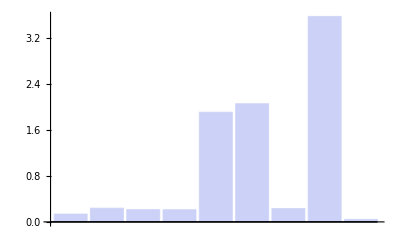

```mathematica
BarChart[Table[Timing[Sudoku[puzzles[[1,i]]]][[1]],{i,9}]]
```

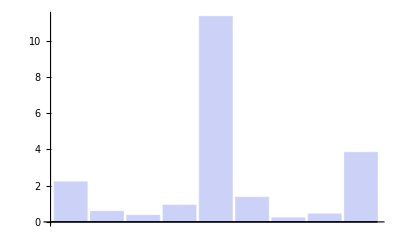

```mathematica
BarChart[Table[Timing[Sudoku[puzzles[[2,i]]]][[1]],{i,9}]]
```